```mathematica
(***  Mathematica modules for the near-exact p.d.f.'s (probability density functions) and c.d.f.'s (cumulative distribution functions) of the l.r.t. (likelihood ratio test) statistics Lambda_4 (L4) and Lambda_5 (L5) in Sections III and IV, and their negative logarithms (according to the developments in Section V)   ***)

(***  Also modules are provided for the near-exact c.f.'s (characteristic functions) of the negative logarithms of all three l.r.t. statistics, mainly because from these it is very easy to obtain the values for the moments of the corresponding l.r.t. statistics, by computing these on 1*I, 2*I, ..., in order to btain the first, second, ..., non-central moments of the l.r.t. statistic     ***)

$MaxExtraPrecision=500;

Off[Solve::ratnz];

(*  Base Module for the computation of the coefficients c_{j,k} in the p.d.f. and c.d.f. of the GIG (Generalized Integer Gamma) and the GNIG (Generalized Near-Integer Gamma) distributions   *)

Makec[r_,l_,p_]:=Module[{c},
c=Table[Table[1,{j,1,Max[r]}],{i,1,p}];
Table[c=ReplacePart[c,(Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,1,i-1}]*Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,i+1,p}])/(r[[i]]-1)!,{i,r[[i]]}],{i,1,p}];
Table[Table[c=ReplacePart[c,Sum[((r[[i]]-k+j-1)!*(Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,1,i-1}]+Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,i+1,p}])*c[[i]][[r[[i]]-(k-j)]])/(r[[i]]-k-1)!,{j,1,k}]/k,{i,r[[i]]-k}],{k,1,r[[i]]-1}],{i,1,p}];
c
]

(*  Module for the p.d.f. of the GIG (Generalized Integer Gamma distribution  *)

GIGpdf[r_,li_,z_]:=Module[{p,l},If[Count[r,_Integer]==Length[r]&&And@@Positive[r]&&And@@Positive[li]&&Length[r]==Length[li],
p=Length[r];
l=Rationalize[li,0];
c=Makec[r,l,p];
Product[l[[j]]^r[[j]],{j,1,p}]*Sum[Exp[-l[[j]]*z]*Sum[c[[j]][[k]]*z^(k-1),{k,1,r[[j]]}],{j,1,p}]
]
]

(*  Module for the c.d.f. of the GIG (Generalized Integer Gamma distribution  *)

GIGcdf[r_,li_,z_]:=Module[{p,l,c},If[Count[r,_Integer]==Length[r]&&And@@Positive[r]&&And@@Positive[li]&&Length[r]==Length[li],
p=Length[r];
l=Rationalize[li,0];
c=Makec[r,l,p];
1-Product[l[[j]]^r[[j]],{j,1,p}]*Sum[Exp[-l[[j]]*z]*Sum[c[[j]][[k]]*(k-1)!*Sum[z^i/(i!*l[[j]]^(k-i)),{i,0,k-1}],{k,1,r[[j]]}],{j,1,p}]
]
]


(*  Module for the p.d.f. of the GNIG (Generalized Near-Integer Gamma distribution  *)

GNIGpdf[rj_,ri_,lji_,li_,z_]:=Module[{p,lj,l,r,c},
If[Count[rj,_Integer]==Length[rj]&&And@@Positive[rj]&&And@@Positive[lji]&&Length[rj]==Length[lji]&&ri>0&&li>0,
p=Length[rj];
lj=Rationalize[lji,0];
l=Rationalize[li,0];
r=Rationalize[ri,0];
c=Makec[rj,lj,p];
Product[lj[[j]]^rj[[j]],{j,1,p}]*l^r*Sum[Exp[-lj[[j]]*z]*Sum[c[[j]][[k]]*Gamma[k]/Gamma[k+r]*z^(k+r-1)*Hypergeometric1F1[r,k+r,-(l-lj[[j]])*z],{k,1,rj[[j]]}],{j,1,p}]
]
]


(*  Module for the c.d.f. of the GNIG (Generalized Near-Integer Gamma distribution  *)

GNIGcdf[rj_,ri_,lji_,li_,z_]:=Module[{p,lj,l,r,c},
If[Count[rj,_Integer]==Length[rj]&&And@@Positive[rj]&&And@@Positive[lji]&&Length[rj]==Length[lji]&&ri>0&&li>0,
p=Length[rj];
lj=Rationalize[lji,0];
l=Rationalize[li,0];
r=Rationalize[ri,0];
c=Makec[rj,lj,p];
l^r*z^r/Gamma[r+1]*Hypergeometric1F1[r,r+1,-l*z]-Product[lj[[j]]^rj[[j]],{j,1,p}]*l^r*Sum[Exp[-lj[[j]]*z]*Sum[c[[j]][[k]]/lj[[j]]^k*Gamma[k]*Sum[z^(r+i)*lj[[j]]^i/Gamma[r+1+i]*Hypergeometric1F1[r,r+1+i,-(l-lj[[j]])*z],{i,0,k-1}],{k,1,rj[[j]]}],{j,1,p}]
]
]


(*  c.f. of a general mixture of Gamma distributions   *)

FCMG[p_,r_,m_,t_]:=Module[{},
c=Length[p];
pp=Sum[p[[j]],{j,1,c}];
Sum[p[[j]]*m[[j]]^r[[j]]*(m[[j]]-I*t)^(-r[[j]]),{j,1,c}]+(1-pp)*m[[1+c]]^r[[1+c]]*(m[[1+c]]-I*t)^(-r[[1+c]])
]

(*  Module for the computation of the moments of a general mixture of Gamma distributions  *)

MomMG[p_,r_,m_,h_]:=Module[{},
c=Length[p];
pp=Sum[p[[j]],{j,1,c}];
Sum[p[[j]]/m[[j]]^h*Product[(r[[j]]+i),{i,0,h-1}],{j,1,c}]+(1-pp)/m[[1+c]]^h*Product[(r[[1+c]]+i),{i,0,h-1}]
]



(*****   Modules for the c.f. and moments of the negative logarithm of the l.r.t. statistic for the sphericity test    *****)
(*****   All modules have three mandatory arguments (in this order): i) the sample size, ii) the number of variables, iii) the running variable for the function   *****)

(*  Module for the part of the exact c.f. (characteristic function) of the negative logarithm of the l.r.t. (likelihood ratio test) statistic for the sphericity test which is left unchanged  *)

CFW4P1[n_,p_,t_]:=Product[((n-j-1)/n)^(p-j)*((n-j-1)/n-I*t)^(-(p-j)),{j,1,p-1}]

(*  Module for the part of the exact c.f. (characteristic function) of the negative logarithm of the l.r.t. (likelihood ratio test) statistic for the sphericity test which is to be asymptotically approximated  *)

CFW4P2[n_,p_,t_]:=Product[Gamma[n-1+j/p]/Gamma[n-1]*Gamma[n-1-n*I*t]/Gamma[n-1+j/p-n*I*t],{j,1,p-1}]

(*  Module for the whole exact c.f. (characteristic function) of the negative logarithm of the l.r.t. (likelihood ratio test) statistic for the sphericity test   *)

CFW4[n_,p_,t_]:=CFW4P1[n,p,t]*CFW4P2[n,p,t]

(*  Module for the computation of the moments corresponding to the part of the c.f. (characteristic function) CFW4P2  *)

MomW4P2[n_,p_,h_]:=D[I^(-h)*CFW4P2[n,p,t],{t,h}]/.t->0



(*****    Modules for the near-exact distributions for the l.r.t. statistic for the test of sphericity    *****)
(*****    All modules have as mandatory arguments (in this order): i) the number of variables, ii) the sample size, iii) the number of exact moments to be matched, iv) the running variable for the function and a fifth, optional, argument which is the number of precision digits used to compute the exact moments to be matched (by default this value is 100)   *****)


(*  Module for the computation/implementation of the c.f. of the near-exact distribution for W4, the negative logarithm of the l.r.t. statistic for the sphericity test    *)

NECFW4[p_,n_,m_,t_,prec_:100]:=Module[{mom,r,lamb,ppp},
mom=Table[SetPrecision[MomW4P2[n,p,h],prec],{h,1,m}];
Clear[pe];
r=(p-1)/2;
lamb=(n-1)/n;
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
Solve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
CFW4P1[n,p,t]*FCMG[ppp,Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],t]
]

(*  Module for the computation/implementation of the p.d.f. of the near-exact distribution for the negative logarithm of the l.r.t. statistic for the sphericity test    *)

NEPDFW4[p_,n_,m_,z_,prec_:100]:=Module[{mom,r,lamb,ppp},
mom=Table[SetPrecision[MomW4P2[n,p,h],prec],{h,1,m}];
Clear[pe];
r=(p-1)/2;
lamb=(n-1)/n;
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
Solve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
tp=Total[ppp];
rj=Table[p-j,{j,1,p-1}];
lj=Table[(n-j)/n,{j,2,p}];
If[Mod[p,2]==0,Sum[ppp[[j]]*GNIGpdf[rj,r+j-1,lj,lamb,z],{j,1,m}]+(1-tp)*GNIGpdf[rj,r+m,lj,lamb,z],Sum[ppp[[j]]*GIGpdf[Flatten[{rj,{r+j-1}}],Flatten[{lj,{lamb}}],z],{j,1,m}]+(1-tp)*GIGpdf[Flatten[{rj,{r+m}}],Flatten[{lj,{lamb}}],z]]
] 


(*  Module for the computation/implementation of the c.d.f. of the near-exact distribution for the negative logarithm of the l.r.t. statistic for the sphericity test    *)

NECDFW4[p_,n_,m_,z_,prec_:100]:=Module[{mom,r,lamb,ppp},
mom=Table[SetPrecision[MomW4P2[n,p,h],prec],{h,1,m}];
Clear[pe];
r=(p-1)/2;
lamb=(n-1)/n;
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
Solve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
tp=Total[ppp];
rj=Table[p-j,{j,1,p-1}];
lj=Table[(n-j)/n,{j,2,p}];
If[Mod[p,2]==0,Sum[ppp[[j]]*GNIGcdf[rj,r+j-1,lj,lamb,z],{j,1,m}]+(1-tp)*GNIGcdf[rj,r+m,lj,lamb,z],Sum[ppp[[j]]*GIGcdf[Flatten[{rj,{r+j-1}}],Flatten[{lj,{lamb}}],z],{j,1,m}]+(1-tp)*GIGcdf[Flatten[{rj,{r+m}}],Flatten[{lj,{lamb}}],z]]
]

(*  Module for the computation/implementation of the p.d.f. of the near-exact distribution for the l.r.t. statistic for the sphericity test, Lambda_4 (L4)    *)

(* NEPDFL4[p_,n_,m_,z_,prec_:100]:=Module[{mom,r,lamb,ppp},
mom=Table[SetPrecision[MomW4P2[n,p,h],prec],{h,1,m}];
Clear[pe];
r=(p-1)/2;
lamb=(n-1)/n;
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
NSolve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
tp=Total[ppp];
rj=Table[p-j,{j,1,p-1}];
lj=Table[(n-j)/n,{j,2,p}];
If[Mod[p,2]==0,Sum[ppp[[j]]*GNIGpdf[rj,r+j-1,lj,lamb,-Log[z]]*1/z,{j,1,m}]+(1-tp)*GNIGpdf[rj,r+m,lj,lamb,-Log[z]]*1/z,Sum[ppp[[j]]*GIGpdf[Flatten[{rj,{r+j-1}}],Flatten[{lj,{lamb}}],-Log[z]]*1/z,{j,1,m}]+(1-tp)*GIGpdf[Flatten[{rj,{r+m}}],Flatten[{lj,{lamb}}],-Log[z]]*1/z]
] *)

NEPDFL4[p_,n_,m_,z_,prec_:100]:=NEPDFW4[p,n,m,-Log[z],prec]*1/z

(*  Module for the computation/implementation of the c.d.f. of the near-exact distribution for the l.r.t. statistic for the sphericity test, Lambda_4 (L4)    *)

(* NECDFL4[p_,n_,m_,z_,prec_:100]:=Module[{mom,r,lamb,ppp},
mom=Table[SetPrecision[MomW4P2[n,p,h],prec],{h,1,m}];
Clear[pe];
r=(p-1)/2;
lamb=(n-1)/n;
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
NSolve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
tp=Total[ppp];
rj=Table[p-j,{j,1,p-1}];
lj=Table[(n-j)/n,{j,2,p}];
If[Mod[p,2]==0,Sum[ppp[[j]]*(1-GNIGcdf[rj,r+j-1,lj,lamb,-Log[z]]),{j,1,m}]+(1-tp)*(1-GNIGcdf[rj,r+m,lj,lamb,-Log[z]]),Sum[ppp[[j]]*(1-GIGcdf[Flatten[{rj,{r+j-1}}],Flatten[{lj,{lamb}}],-Log[z]]),{j,1,m}]+(1-tp)*(1-GIGcdf[Flatten[{rj,{r+m}}],Flatten[{lj,{lamb}}],-Log[z]])]
] *)

NECDFL4[p_,n_,m_,z_,prec_:100]:=1-NECDFW4[p,n,m,-Log[z],prec]


(*****   Modules for the c.f. and moments of the negative logarithm of the l.r.t. statistic for the test of equality of covariance matrices    *****)


(*  Module for the part of the exact c.f. of the negative logarithm of the l.r.t. statistic for the test of equality of covariance matrices which is left unchanged  *)

CFW51[n_,p_,q_,t_]:=Module[{},
rj=Table[0,{j,1,p-1}];
Do[rj[[j]]=q*(q-1)*(j-1/2),{j,1,Ceiling[(p-1)/q]-1}];
rj[[Ceiling[(p-1)/q]]]=1/2*(p-p^2+2*p*q*Ceiling[(p-1)/q]+q-3*Ceiling[(p-1)/q]*q-q^2*(Ceiling[(p-1)/q]-1)^2);
Do[rj[[j]]=q*(p-j),{j,1+Ceiling[(p-1)/q],p-1}];
Product[((n-1-j)/n)^rj[[j]]*((n-1-j)/n-I*t)^(-rj[[j]]),{j,1,p-1}]
]

(*  Module for the part of the exact c.f. of the negative logarithm of the l.r.t. statistic for the test of equality of covariance matrices which is to be asymptotically approximated  *)

CFW52[n_,p_,q_,t_]:=Product[Product[Gamma[n+(k-j)/q]/Gamma[n+Floor[(k-j)/q]]*Gamma[n+Floor[(k-j)/q]-n*I*t]/Gamma[n+(k-j)/q-n*I*t],{k,1,q}],{j,1,p}]

(*  Module for the whole exact c.f. of the negative logarithm of the l.r.t. statistic for the test of equality of covariance matrices  *)

CFW5[n_,p_,q_,t_]:=CFW51[n,p,q,t]*CFW52[n,p,q,t]

(*  Module for the computation of the moments corresponding to the part of the c.f. (characteristic function) CFW52  *)

MomCFW52[n_,p_,q_,h_]:=I^(-h)*D[CFW52[n,p,q,t],{t,h}]/.t->0

(*****    Modules for the near-exact distributions for the l.r.t. statistic for the test of equality of covariance matrices    *****)
(*****    All modules have as mandatory arguments (in this order): i) the number of variables, ii) the number of matrices or populations, iii) the sample size, iv) the number of exact moments to be matched, v) the running variable for the function and a sixth, optional, argument which is the number of precision digits used to compute the exact moments to be matched (by default this value is 100)   *****)

(*  Module for the computation/implementation of the c.f. of the near-exact distribution for the negative logarithm of the l.r.t. statistic for the test of equality of covariance matrices    *)

NECFW5[p_,q_,n_,m_,t_,prec_:100]:=Module[{mom,r,lamb,p1,r1,r2,ppp},
mom=Table[SetPrecision[MomCFW52[n,p,q,h],prec],{h,1,m}];
Clear[pe];
r=p*(q-1)/2;
{p1,r1,r2,lamb}=Sort[Cases[{p1,r1,r2,lamb}/.Solve[Table[MomMG[{p1},{r1,r2},{lamb,lamb},h]==mom[[h]],{h,1,4}],{p1,r1,r2,lamb}],{_Real,_Real,_Real,_Real}]][[2]];
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
NSolve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
CFW51[n,p,q,t]*FCMG[ppp,Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],t]
]


(*  Module for the computation/implementation of the p.d.f. of the near-exact distribution for the negative logarithm of the l.r.t. statistic for the test of equality of covariance matrices    *)

NEPDFW5[p_,q_,n_,m_,z_,prec_:100]:=Module[{mom,r,lamb,p1,r1,r2,ppp},
mom=Table[SetPrecision[MomCFW52[n,p,q,h],prec],{h,1,m}];
Clear[pe];
r=p*(q-1)/2;
{p1,r1,r2,lamb}=Sort[Cases[{p1,r1,r2,lamb}/.Solve[Table[MomMG[{p1},{r1,r2},{lamb,lamb},h]==mom[[h]],{h,1,4}],{p1,r1,r2,lamb}],{_Real,_Real,_Real,_Real}]][[2]];
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
NSolve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
tp=Total[ppp];
rj=Flatten[{Table[q*(q-1)*(j-1/2),{j,1,Ceiling[(p-1)/q]-1}],{1/2*(p-p^2+2*Ceiling[(p-1)/q]*p*q+q-3*Ceiling[(p-1)/q]*q-q^2*(Ceiling[(p-1)/q]-1)^2)},Table[q*(p-j),{j,Ceiling[(p-1)/q]+1,p-1}]}];
lj=Table[(n-j)/n,{j,2,p}];
If[Mod[q,2]==0,Sum[ppp[[j]]*GNIGpdf[rj,r+j-1,lj,lamb,z],{j,1,m}]+(1-tp)*GNIGpdf[rj,r+m,lj,lamb,z],Sum[ppp[[j]]*GIGpdf[Flatten[{rj,{r+j-1}}],Flatten[{lj,{lamb}}],z],{j,1,m}]+(1-tp)*GIGpdf[Flatten[{rj,{r+m}}],Flatten[{lj,{lamb}}],z]]
]


(*  Module for the computation/implementation of the c.d.f. of the near-exact distribution for the negative logarithm of the l.r.t. statistic for the test of equality of covariance matrices    *)

NECDFW5[p_,q_,n_,m_,z_,prec_:100]:=Module[{mom,r,lamb,p1,r1,r2,ppp},
mom=Table[SetPrecision[MomCFW52[n,p,q,h],prec],{h,1,m}];
Clear[pe];
r=p*(q-1)/2;
{p1,r1,r2,lamb}=Sort[Cases[{p1,r1,r2,lamb}/.Solve[Table[MomMG[{p1},{r1,r2},{lamb,lamb},h]==mom[[h]],{h,1,4}],{p1,r1,r2,lamb}],{_Real,_Real,_Real,_Real}]][[2]];
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
NSolve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
tp=Total[ppp];
rj=Flatten[{Table[q*(q-1)*(j-1/2),{j,1,Ceiling[(p-1)/q]-1}],{1/2*(p-p^2+2*Ceiling[(p-1)/q]*p*q+q-3*Ceiling[(p-1)/q]*q-q^2*(Ceiling[(p-1)/q]-1)^2)},Table[q*(p-j),{j,Ceiling[(p-1)/q]+1,p-1}]}];
lj=Table[(n-j)/n,{j,2,p}];
If[Mod[q,2]==0,Sum[ppp[[j]]*GNIGcdf[rj,r+j-1,lj,lamb,z],{j,1,m}]+(1-tp)*GNIGcdf[rj,r+m,lj,lamb,z],Sum[ppp[[j]]*GIGcdf[Flatten[{rj,{r+j-1}}],Flatten[{lj,{lamb}}],z],{j,1,m}]+(1-tp)*GIGcdf[Flatten[{rj,{r+m}}],Flatten[{lj,{lamb}}],z]]
]

(*  Module for the computation/implementation of the p.d.f. of the near-exact distribution for the l.r.t. statistic for the test of equality of covariance matrices, Lambda_5 (L5)    *)

(* NEPDFL5[p_,q_,n_,m_,z_,prec_:100]:=Module[{mom,r,lamb,p1,r1,r2,ppp},
mom=Table[SetPrecision[MomCFW52[n,p,q,h],prec],{h,1,m}];
Clear[pe];
r=p*(q-1)/2;
{p1,r1,r2,lamb}=Sort[Cases[{p1,r1,r2,lamb}/.NSolve[Table[MomMG[{p1},{r1,r2},{lamb,lamb},h]==mom[[h]],{h,1,4}],{p1,r1,r2,lamb}],{_Real,_Real,_Real,_Real}]][[2]];
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
NSolve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
tp=Total[ppp];
rj=Flatten[{Table[q*(q-1)*(j-1/2),{j,1,Ceiling[(p-1)/q]-1}],{1/2*(p-p^2+2*Ceiling[(p-1)/q]*p*q+q-3*Ceiling[(p-1)/q]*q-q^2*(Ceiling[(p-1)/q]-1)^2)},Table[q*(p-j),{j,Ceiling[(p-1)/q]+1,p-1}]}];
lj=Table[(n-j)/n,{j,2,p}];
If[Mod[q,2]==0,Sum[ppp[[j]]*GNIGpdf[rj,r+j-1,lj,lamb,-Log[z]]*1/z,{j,1,m}]+(1-tp)*GNIGpdf[rj,r+m,lj,lamb,-Log[z]]*1/z,Sum[ppp[[j]]*GIGpdf[Flatten[{rj,{r+j-1}}],Flatten[{lj,{lamb}}],-Log[z]]*1/z,{j,1,m}]+(1-tp)*GIGpdf[Flatten[{rj,{r+m}}],Flatten[{lj,{lamb}}],-Log[z]]*1/z]
] *)

NEPDFL5[p_,q_,n_,m_,z_,prec_:100]:=NEPDFW5[p,q,n,m,-Log[z],prec]*1/z


(*  Module for the computation/implementation of the c.d.f. of the near-exact distribution for the l.r.t. statistic for the test of equality of covariance matrices, Lambda_5 (L5)    *)

(* NECDFL5[p_,q_,n_,m_,z_,prec_:100]:=Module[{mom,r,lamb,p1,r1,r2,ppp},
mom=Table[SetPrecision[MomCFW52[n,p,q,h],prec],{h,1,m}];
Clear[pe];
r=p*(q-1)/2;
{p1,r1,r2,lamb}=Sort[Cases[{p1,r1,r2,lamb}/.NSolve[Table[MomMG[{p1},{r1,r2},{lamb,lamb},h]==mom[[h]],{h,1,4}],{p1,r1,r2,lamb}],{_Real,_Real,_Real,_Real}]][[2]];
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,m}]/.
NSolve[Table[mom[[h]]==MomMG[Table[pe[[j]],{j,1,m}],Table[r+i,{i,0,m}],Table[lamb,{i,1,m+1}],h],{h,1,m}],Table[pe[[j]],{j,1,m}]]];
tp=Total[ppp];
rj=Flatten[{Table[q*(q-1)*(j-1/2),{j,1,Ceiling[(p-1)/q]-1}],{1/2*(p-p^2+2*Ceiling[(p-1)/q]*p*q+q-3*Ceiling[(p-1)/q]*q-q^2*(Ceiling[(p-1)/q]-1)^2)},Table[q*(p-j),{j,Ceiling[(p-1)/q]+1,p-1}]}];
lj=Table[(n-j)/n,{j,2,p}];
If[Mod[q,2]==0,Sum[ppp[[j]]*(1-GNIGcdf[rj,r+j-1,lj,lamb,-Log[z]]),{j,1,m}]+(1-tp)*(1-GNIGcdf[rj,r+m,lj,lamb,-Log[z]]),Sum[ppp[[j]]*(1-GIGcdf[Flatten[{rj,{r+j-1}}],Flatten[{lj,{lamb}}],-Log[z]]),{j,1,m}]+(1-tp)*(1-GIGcdf[Flatten[{rj,{r+m}}],Flatten[{lj,{lamb}}],-Log[z]])]
] *)

NECDFL5[p_,q_,n_,m_,z_,prec_:100]:=1-NECDFW5[p,q,n,m,-Log[z],prec]
```

```mathematica
(*****   Examples of use which work also as 'verifications'   *****)
```

```mathematica
(*   For Lambda_4  and  W4  *)
```

```mathematica
p=4;
n=25;
m=4;
CF4[t_]:=NECFW4[p,n,m,t];
PDF4[z_]:=NEPDFW4[p,n,m,z];
CDF4[z_]:=NECDFW4[p,n,m,z];
```

```mathematica
(*  2nd exact moment of W4  *)
```

```mathematica
SetPrecision[I^(-2)*D[CFW4[n,p,t],{t,2}]/.t->0,100]
```

236.38141880553610998472962943765741961333523648161249416343941332657176695877825119072614909207

```mathematica
(*  2nd near-exact moment of W4 (equal to the exact moment, since m=4 exact moments of W4 are matched by the near-exact distribution   *)
```

```mathematica
I^(-2)*D[CF4[t],{t,2}]/.t->0
```

78.092375102263279643972598386412611428030167310039225373239554367601585872203106492

```mathematica
NIntegrate[PDF4[z]*z^2,{z,0,10000},WorkingPrecision->60,MaxRecursion->16]
```

78.0923751022632796439725983864126114280301673100392253732396

```mathematica
(*  On the relation between near-exact p.d.f. and c.d.f.  *)
```

```mathematica
N[NIntegrate[PDF4[y],{y,0,123/10},WorkingPrecision->60],55]
```

0.8979159885086214335079972946699120164297273724704113309

```mathematica
N[CDF4[123/10],55]
```

0.8979159885086214335079972946699120164297273724704113309

```mathematica
(*  The 2nd near-exact moment of Lambda_4  *)
```

```mathematica
N[NIntegrate[NEPDFL4[p,n,m,z]*z^2,{z,0,1},WorkingPrecision->60,MaxRecursion->16],55]
```

0.0001581266240315510094942637996423775288923764131783474453

```mathematica
N[SetPrecision[NECFW4[p,n,m,2*I],60],55]
```

0.0001581266240315510094942637996423775288923764131783474453

```mathematica
(*  The 2nd exact moment of Lambda_4  (note that the moments that are matched by the near-exact distributions are moments of W4  *)
```

```mathematica
SetPrecision[CFW4[n,p,2*I],60]
```

0.000158126624023714210487091506622829310190144354146630328261

```mathematica
(*  On the relation between the near-exact p.d.f. and c.d.f. of Lambda_4  *)
```

```mathematica
SetPrecision[NEPDFL4[p,n,m,1/1000],125]
SetPrecision[D[NECDFL4[p,n,m,z],z]/.z->1/1000,125]
```

138.81735878802042973643574613671067645782283104294152875865877129689717921030095781279546817741785022304163867961828272822762

138.81735878802042973643574613671067645782283104294152875865877129689717921030095781279546817741785022304163924454043324138699

```mathematica
(*  Since above, after a given number of decimal places there is some disagreement between the values for the p.d.f. and the derivative of the c.d.f., we try here 200 digits of precision in the computation of the exact moments used to compute the near-exact distribution, instead of the default 100 precision digits  *)
(* However, note that version 7 gives more precise results than version 9 - See the version 7 files !!!  *)
```

```mathematica
SetPrecision[NEPDFL4[p,n,m,1/1000,200],200]
SetPrecision[D[NECDFL4[p,n,m,z,200],z]/.z->1/1000,200]
```

138.81735878802042973643574613671067645782283104294152875865877129689717921030095781279546817741785022242452226047082029095944215053299035641277660099082750748671723813975896139729495920956096917465246

138.81735878802042973643574613671067645782283104294152875865877129689717921030095781279546817741785022242452226047082029095944215053299035641277660099082750748671723813975896139729495920956096917465246

```mathematica
(*  Plots of the pdf and cdf of W4   *)
```

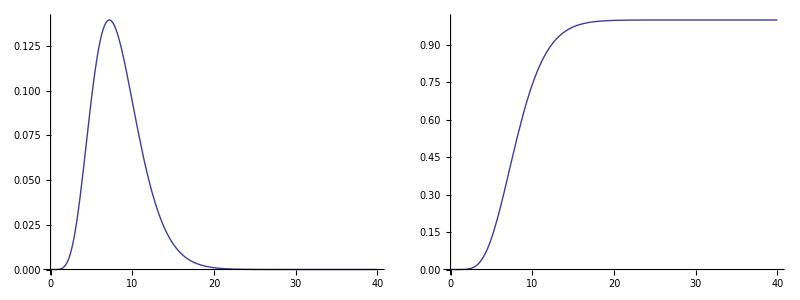

```mathematica
Grid[{{Plot[SetPrecision[NEPDFW4[p,n,4,Rationalize[z,0]],40],{z,0,40},PlotRange->All],Plot[SetPrecision[NECDFW4[p,n,4,Rationalize[z,0]],40],{z,0,40}]}}]
```

```mathematica
(*   For Lambda_5  and  W5  *)
```

```mathematica
p=5;
q=3;
n=12;
m=4;
CF5[t_]:=NECFW5[p,q,n,m,t];
PDF5[z_]:=NEPDFW5[p,q,n,m,z];
CDF5[z_]:=NECDFW5[p,q,n,m,z];
```

```mathematica
(*  2nd exact moment of W5  *)
```

```mathematica
SetPrecision[I^(-2)*D[CFW5[n,p,q,t],{t,2}]/.t->0,100]
```

1197.6995991067065989423494594048252785995389195436274082636975341664793119938925785320832709321

```mathematica
(*  2nd near-exact moment of W5 (equal to the exact moment, since m=4 exact moments of W5 are matched by the near-exact distribution   *)
```

```mathematica
SetPrecision[I^(-2)*D[CF5[t],{t,2}]/.t->0,60]
```

1197.6995991067065989423494594048252785995389195436274082637

```mathematica
NIntegrate[PDF5[z]*z^2,{z,0,10^5},MaxRecursion->20,WorkingPrecision->60]
```

1197.6995991067065989423494594048252785995389195436274082637

```mathematica
(*  On the relation between near-exact p.d.f. and c.d.f.  *)
```

```mathematica
N[NIntegrate[PDF5[z],{z,0,123/10},WorkingPrecision->65],55]
SetPrecision[CDF5[123/10],55]
```

0.00001083061290123352261496841762278611922123607851853660525

0.00001083061290123352261496841762278611922123607851853660525

```mathematica
(*  The 2nd near-exact moment of Lambda_5  *)
```

```mathematica
NIntegrate[NEPDFL5[p,q,n,m,z]*z^2,{z,0,1},MaxRecursion->20,WorkingPrecision->60]
SetPrecision[NECFW5[p,q,n,m,2*I],60]
```

6.49018526092499064645225413397642257412410029389877712528807×10^-15

6.49018526092499064645225413397642257412410029389877712528807×10^-15

```mathematica
(*  On the relation between the near-exact p.d.f. and c.d.f. of Lambda_5  *)
```

```mathematica
SetPrecision[NEPDFL5[p,q,n,m,1/1000],85]
SetPrecision[D[NECDFL5[p,q,n,m,z],z]/.z->1/1000,85]
SetPrecision[NEPDFL5[p,q,n,m,1/1000],100]
SetPrecision[D[NECDFL5[p,q,n,m,z],z]/.z->1/1000,100]
```

7.854601486277427611532577302430262034724708671612492161219446820499982674069305867245×10^-7

7.854601486277427611532577302430262034724708671612492161219446820499982674069305867245×10^-7

7.854601486277427611532577302430262034724708671612492161219446820499982674069305867244647601910800649×10^-7

7.854601486277427611532577302430262034724708671612492161219446820499982674069305867244647606592477004×10^-7

```mathematica
(*  Since above, after a given number of decimal places there is some disagreement between the values for the p.d.f. and the derivative of the c.d.f., we try here 200 digits of precision in the computation of the exact moments used to compute the near-exact distribution, instead of the default 100 precision digits  *)
```

```mathematica
SetPrecision[NEPDFL5[p,q,n,m,1/1000,200],200]
SetPrecision[D[NECDFL5[p,q,n,m,z,200],z]/.z->1/1000,200]
SetPrecision[NEPDFL5[p,q,n,m,1/1000,200],220]
SetPrecision[D[NECDFL5[p,q,n,m,z,200],z]/.z->1/1000,220]
```

7.8546014862774276115325773024302620347247086716124921612194468204999826740694361348338449529971547921698921640078620719575608053596323076724177342156629889335103917034499568964601494091725027222744052×10^-7

7.8546014862774276115325773024302620347247086716124921612194468204999826740694361348338449529971547921698921640078620719575608053596323076724177342156629889335103917034499568964601494091725027222744052×10^-7

7.854601486277427611532577302430262034724708671612492161219446820499982674069436134833844952997154792169892164007862071957560805359632307672417734215662988933510391703449956896460149409172502722274405187745059882929898543×10^-7

7.854601486277427611532577302430262034724708671612492161219446820499982674069436134833844952997154792169892164007862071957560805359632307672417734215662988933510391703449956896460149409172502722274405187663075309133419775×10^-7

```mathematica
(*  Plots of the pdf and cdf of W5   *)
```

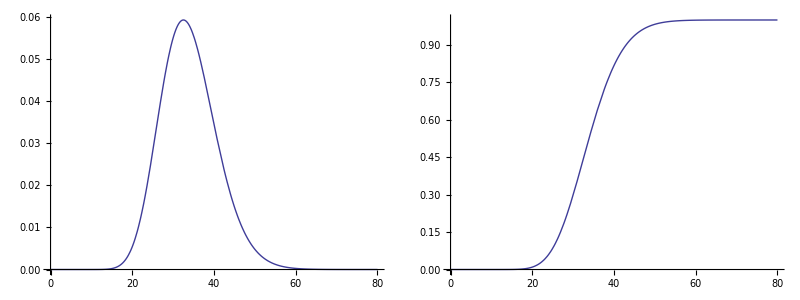

```mathematica
Grid[{{Plot[SetPrecision[NEPDFW5[p,q,n,4,Rationalize[z,0]],40],{z,0,80},PlotRange->All],Plot[SetPrecision[NECDFW5[p,q,n,4,Rationalize[z,0]],40],{z,0,80}]}}]
```